```mathematica
从P倒推需要的Mdot
假设现在源处于spin equilibrium，又现在的周期P推出此时的Mdot，并由此倒推初始盘的质量和回落盘形成时间;
P1=1.427579,Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403,Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316,Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042,Pdot4=-4.7*^-9;MJD4=56851.5;
MJD in units of day;
```

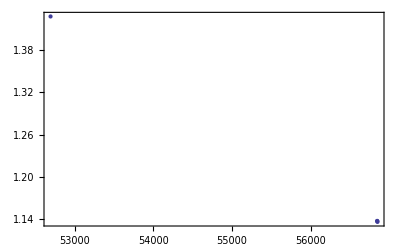

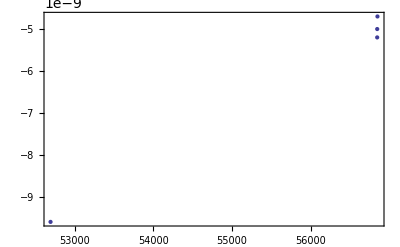

```mathematica
P1=1.427579;Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;
P=List[P1,P2,P3,P4];
Pdot=List[Pdot1,Pdot2,Pdot3,Pdot4];
MJD=List[MJD1,MJD2,MJD3,MJD4];
PandMJD=List[MJD,P]//Transpose;
PdotandMJD=List[MJD,Pdot]//Transpose;
ListPlot[PandMJD,Frame->True]
ListPlot[PdotandMJD,Frame->True]
(*[[2;;4]]*)
```

```mathematica
Clear["`*"]
G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;
m=1.4;
MdotEdd=1.39*10^18*m;(*Eddington accretion rate*)
M=m*Msun;
Irot=10^45;
xi=0.5;

P1=1.427579;Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;
P=List[P1,P2,P3,P4];
Pdot=List[Pdot1,Pdot2,Pdot3,Pdot4];
torque1=-2*Pi*Irot*Pdot/P^2

B={B1,B2,B3,B4};
Mdot={Mdot1,Mdot2,Mdot3,Mdot4};
mu=0.5*B*R^3;
Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);
torque2=Mdot*(G*M*Rin)^(1/2)

Table[i;Solve[torque2[[i]]==torque1[[i]],{B[[i]],Mdot[[i]]}],{i,1,4}]
(*Solve[torque2==torque1,{B,Mdot}]*)

(*MJD=List[MJD1,MJD2,MJD3,MJD4];
PandMJD=List[MJD,P]//Transpose;
ListLinePlot[PandMJD[[2;;4]]]*)
```

{2.95972×10^37,2.52554×10^37,2.42878×10^37,2.28817×10^37}

{1.39301×10^16 (B1^4/Mdot1^2)^(1/14) Mdot1,1.39301×10^16 (B2^4/Mdot2^2)^(1/14) Mdot2,1.39301×10^16 (B3^4/Mdot3^2)^(1/14) Mdot3,1.39301×10^16 (B4^4/Mdot4^2)^(1/14) Mdot4}

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve :: svars will be suppressed during this calculation.

{{{Mdot1→-(7.61811×10^24)/B1^(1/3)},{Mdot1→-(0.+7.61811×10^24 ⅈ)/B1^(1/3)},{Mdot1→(0.+7.61811×10^24 ⅈ)/B1^(1/3)},{Mdot1→(7.61811×10^24)/B1^(1/3)}},{{Mdot2→-(6.33094×10^24)/B2^(1/3)},{Mdot2→-(0.+6.33094×10^24 ⅈ)/B2^(1/3)},{Mdot2→(0.+6.33094×10^24 ⅈ)/B2^(1/3)},{Mdot2→(6.33094×10^24)/B2^(1/3)}},{{Mdot3→-(6.04886×10^24)/B3^(1/3)},{Mdot3→-(0.+6.04886×10^24 ⅈ)/B3^(1/3)},{Mdot3→(0.+6.04886×10^24 ⅈ)/B3^(1/3)},{Mdot3→(6.04886×10^24)/B3^(1/3)}},{{Mdot4→-(5.64233×10^24)/B4^(1/3)},{Mdot4→-(0.+5.64233×10^24 ⅈ)/B4^(1/3)},{Mdot4→(0.+5.64233×10^24 ⅈ)/B4^(1/3)},{Mdot4→(5.64233×10^24)/B4^(1/3)}}}

```mathematica
{Mdot1->(7.618111583662568*^24)/B1^(1/3)};
{Mdot2->(6.330941226343839*^24)/B2^(1/3)};
{Mdot3->(6.048860474336591*^24)/B3^(1/3)};
{Mdot4->(5.642330295355947*^24)/B4^(1/3)};
```

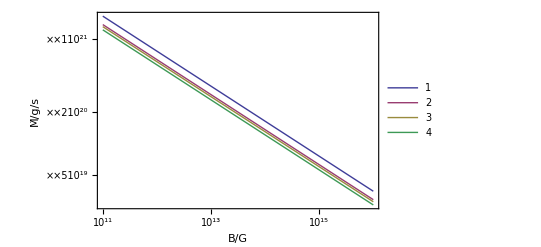

```mathematica
Clear["`*"]
k1=7.61811;k2=6.33094;k3=6.04886;k4=5.64233;
Mdot1=k1*10^24/B^(1/3);
Mdot2=k2*10^24/B^(1/3);
Mdot3=k3*10^24/B^(1/3);
Mdot4=k4*10^24/B^(1/3);
LogLogPlot[{Mdot1,Mdot2,Mdot3,Mdot4},{B,10^11,10^16},Frame->True,FrameLabel->{"B/G","Ṁ/g/s"},PlotLegends->{"1","2","3","4"}]
```

```mathematica
Clear["`*"]
B=10^15;
k1=7.61811;k2=6.33094;k3=6.04886;k4=5.64233;
Mdot1=k1*10^24/B^(1/3);
Mdot2=k2*10^24/B^(1/3);
Mdot3=k3*10^24/B^(1/3);
Mdot4=k4*10^24/B^(1/3);
Mdot=List[Mdot1,Mdot2,Mdot3,Mdot4];
Mean[Mdot]
```

6.41006×10^19

```mathematica
so alpha maybe euqals -8/7;
```

```mathematica
Mdot=Mdot0*(t/t0)^-alpha
```

```mathematica
Clear["`*"]
P1=1.427579;Pdot1=-9.6*^-9;MJD1=52690.9;m1=7.61811;
P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;m2=6.33094;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;m3=6.04886;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;m4=5.64233;

P=List[P1,P2,P3,P4];
Pdot=List[Pdot1,Pdot2,Pdot3,Pdot4];
MJD=List[MJD1,MJD2,MJD3,MJD4];

B=10^15;
k1=7.61811;k2=6.33094;k3=6.04886;k4=5.64233;
Mdot1=k1*10^24/B^(1/3);
Mdot2=k2*10^24/B^(1/3);
Mdot3=k3*10^24/B^(1/3);
Mdot4=k4*10^24/B^(1/3);
Mdot=List[Mdot1,Mdot2,Mdot3,Mdot4];

Mdot*(MJD+10^6)^(4/3)
Mean[Mdot*(MJD+10^6)^(4/3)]
```

{8.15796×10^27,6.8153×10^27,6.51164×10^27,6.07403×10^27}

6.88973×10^27

```mathematica
(m4/m3)^(3/4)
(m4/m2)^(3/4)
```

0.949158

0.917261

```mathematica
NSolve[(MJD2+tf)/(MJD4=tf)==(m4/m2)^(3/4),tf]
```

{{tf→-687072.}}

```mathematica
NSolve[(MJD3+tf)/(MJD4=tf)==(m4/m3)^(3/4),tf]
```

{{tf→-1.11814×10^6}}

```mathematica
NSolve[(MJD2+tf)/(MJD3=tf)==(m3/m2)^(3/4),tf]
```

{{tf→-1.69158×10^6}}

```mathematica
NSolve[(MJD1+tf)/(MJD4=tf)==(m4/m1)^(3/4),tf]
```

{{tf→-261335.}}